```mathematica
SetDirectory[NotebookDirectory[]]
<<KnotTheory`
```

/Users/dj/CLionProjects/c-flypes

Loading KnotTheory` version of September 6, 2014, 13:37:37.2841.
Read more at http://katlas.org/wiki/KnotTheory.

```mathematica
Export["knot_txt_files/knot_4_1.txt",PD[Knot[4,1]]]
```

KnotTheory::loading: Loading precomputed data in PD4Knots`.

knot_txt_files/knot_4_1.txt

```mathematica
Export["knot_txt_files/knot_6_1.txt",PD[Knot[6,1]]]
```

knot_txt_files/knot_6_1.txt

```mathematica
Export["knot_txt_files/knot_15_70.txt",PD[Knot[15,Alternating,70]]]
```

knot_txt_files/knot_15_70.txt

```mathematica
Export["knot_txt_files/knot_16_1.txt",PD[Knot[16,Alternating,1]]]
```

KnotTheory::loading: Loading precomputed data in KnotTheory/16A.dts.

KnotTheory::credits: The GaussCode to PD conversion was written by Siddarth Sankaran at the University of Toronto in the summer of 2005.

knot_txt_files/knot_16_1.txt

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[6,1]]
```

20

```mathematica
Length@GetAllFlypesFromPD[PD@Knot[15,Alternating,70]]
```

54

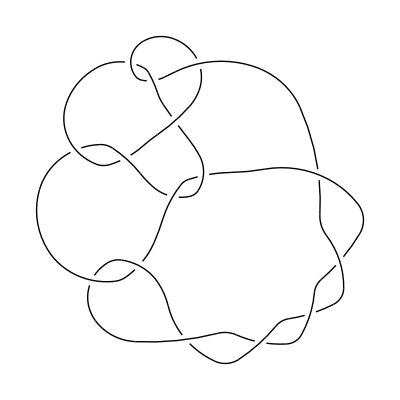

```mathematica
DrawPD[PD@Knot[15,Alternating,70],{Gap->0.03}]
```

```mathematica
Length/@GetAllFlypesFromPD[PD@Knot[6,1]][[All,1]]
```

{2,2,2,2,2,2,3,3,3,3,3,3,4,4,4,4,4,4,4,4}